```mathematica
ASTOR PRIETO DEHGHANPOUR
```

# Pràctica 11: Grafs eulerians i hamiltonians

En aquesta pràctica continuarem utilitzant la llibreria següent.

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

### Grau d’un vèrtex

Donat un graf G, el grau d’un vèrtex v de G és igual al nombre de veïns de v a G. Amb el Mathematica fem servir la instrucció Degrees per trobar la llista dels graus dels vèrtexs 1,2,....

Per exemple:

```mathematica
Ar0={{1,2},{1,3},{2,3},{2,4},{3,5}}
```

{{1,2},{1,3},{2,3},{2,4},{3,5}}

```mathematica
G0=FromUnorderedPairs[Ar0]
```

⁃Graph:<5,5,Undirected>⁃

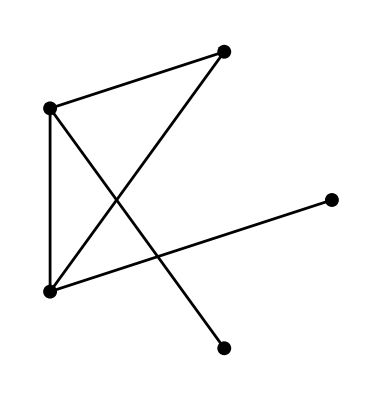

```mathematica
ShowLabeledGraph[G0]
```

```mathematica
Degrees[G0]
```

{2,3,3,1,1}

Per exemple, el grau del vèrtex 4 és

```mathematica
Degrees[G0][[4]]
```

1

Observeu que el Mathematica ens dóna una llista dels graus de tots els vèrtexs.

### Grafs eulerians. Teorema d’Euler

Un recorregut d'un graf es diu que és eulerià si passa per totes les arestes sense repetir-ne cap.
Si un graf té un recorregut eulerià tancat, es diu que és un graf eulerià.
Una caracterització dels grafs eulerians ve donada pel següent teorema d'Euler:

                             TEOREMA D'EULER:
Un graf G connex és eulerià ⟺ Tot vèrtex de G té grau parell

### Exercici

És eulerià G0? “No”.
 Dibuixeu un graf eulerià de 5 vèrtexs amb més de 5 arestes, indicant un circuit d’Euler.

```mathematica
ShowLabeledGraph[G0]
```

-Graphics-

```mathematica
EulerianGraphQ[G0]
```

False

```mathematica
G1 = CompleteGraph[5]
```

⁃Graph:<10,5,Undirected>⁃

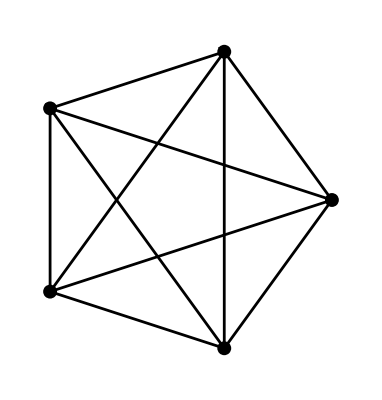

```mathematica
ShowLabeledGraph[G1]
```

```mathematica
EulerianQ[G1]
```

True

```mathematica
SI SERÍA EULERIA!
```

A més a més, amb el Mathematica la instrucció EulerianQ ens diu si un graf és eulerià.

```mathematica
?EulerianQ
```

RowBox[{"EulerianQ", "[", StyleBox["g", "TI"], "]"}] yields True if graph g is Eulerian, meaning there exists a tour that includes each edge exactly once.

### Exercici

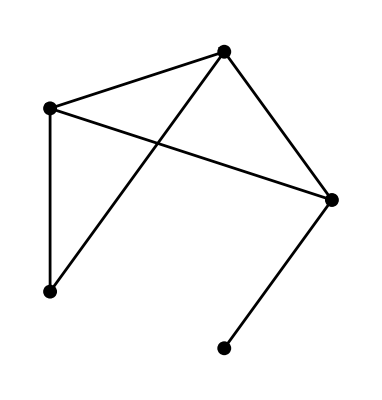
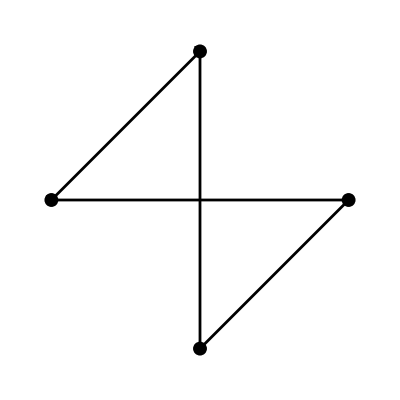
Determineu si els següents grafs són eulerians. En cas afirmatiu doneu-ne un circuit d’Euler.
-Graphics--Graphics-

```mathematica
G3 = FromAdjacencyLists[{{2,3,5},{1,3,5},{1,2},{5},{1,2,4}}]
```

⁃Graph:<6,5,Undirected>⁃

```mathematica
EulerianQ[G3]
```

True

```mathematica
NO ES EULERIA!
```

```mathematica
G4 = FromAdjacencyLists[{{2,3},{1,4},{1,4},{2,3}}]
```

⁃Graph:<4,4,Undirected>⁃

```mathematica
EulerianQ[G4]
```

False

```mathematica
SI ES EULERIA! (GRAU DE TOTS ELS VERTEX PARELLS)
```

### Grafs hamiltonians vs grafs eulerians

Tot i la semblança entre les definicions de graf eulerià i hamiltonià no hi ha cap relació entre elles.

### Exercici

Determineu si els següents grafs són eulerians i/o hamiltonians. Justifuqueu les respostes.

```mathematica
G1=FromUnorderedPairs[{{1,2},{1,3},{2,3},{3,4},{3,5},{4,5}}]
```

⁃Graph:<6,5,Undirected>⁃

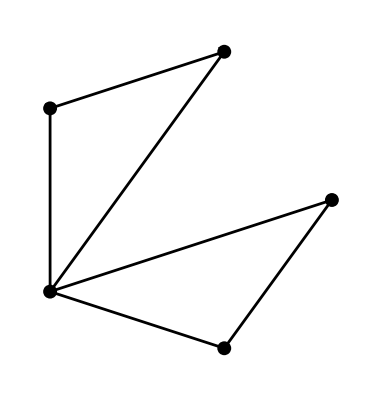

```mathematica
ShowLabeledGraph[G1]
```

```mathematica
Degrees[G1]
```

{2,2,4,2,2}

```mathematica
EULERIA: Si
```

```mathematica
HamiltonianQ[G1]
```

False

```mathematica
HAMILTONIA: No
```

```mathematica
G2=FromUnorderedPairs[{{1,2},{1,4},{1,3},{2,4},{3,4}}]
```

⁃Graph:<5,4,Undirected>⁃

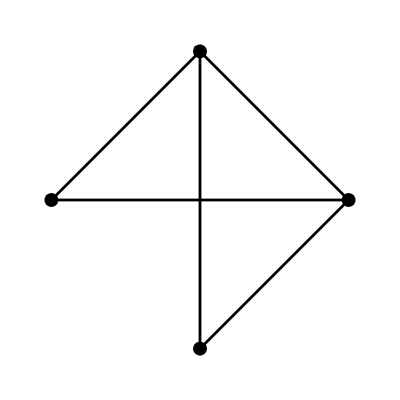

```mathematica
ShowLabeledGraph[G2]
```

```mathematica
Degrees[G2]
```

{3,2,2,3}

```mathematica
EULERIA: No
```

```mathematica
HamiltonianQ[G2]
```

True

```mathematica
HAMILTONIA: Si
```

```mathematica
G3=FromUnorderedPairs[{{1,2},{1,3},{2,3}}]
```

⁃Graph:<3,3,Undirected>⁃

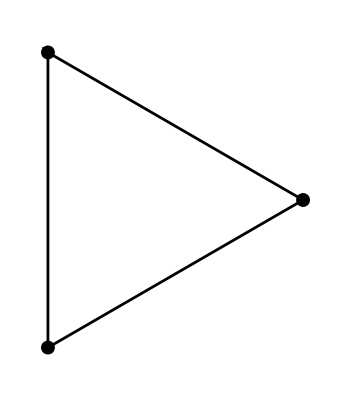

```mathematica
ShowLabeledGraph[G3]
```

```mathematica
Degrees[G3]
```

{2,2,2}

```mathematica
EULERIA: Si
```

```mathematica
HamiltonianQ[G3]
```

True

```mathematica
HAMILTONIAN: Si
```

```mathematica
G4=FromUnorderedPairs[{{1,2},{1,3},{2,3},{3,4}}]
```

⁃Graph:<4,4,Undirected>⁃

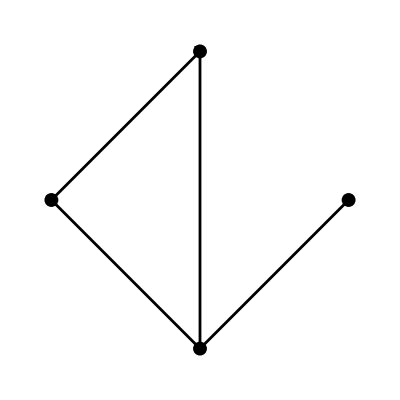

```mathematica
ShowLabeledGraph[G4]
```

```mathematica
Degrees[G4]
```

{2,2,3,1}

```mathematica
EULERIAN: No
```

```mathematica
HamiltonianQ[G4]
```

False

```mathematica
HAMILTONIAN: No
```

#### Grafs hamiltonians. Alguns criteris.

Al contrari del cas eulerià, la llista dels graus dels vèrtexs d’un graf no dóna prou informació per saber si el graf és hamiltonià. 

Definició: En un graf connex, un punt de tall és un vèrtex que satisfà que treient aquest vèrtex i totes les arestes incidents, el graf que en resulta no és connex.

Proposició: Una condició necessària per a que un graf sigui hamiltonià és que no tingui punts de tall.

### Exercici:

Determineu un punt de tall i proveu que el següent graf no és hamiltonià. Comproveu el resultat amb el Mathematica.

```mathematica
El vertex 3 es un punt de tall.
```

```mathematica
H1 = FromAdjacencyLists[{{2,3},{1,3},{1,2,4},{3}}]
```

⁃Graph:<4,4,Undirected>⁃

```mathematica
HamiltonianQ[H1]
```

False

Tanmateix, aquesta condició no és suficient. Per exemple, el graf G5 següent no té punts de tall però no és hamiltonià.

```mathematica
G5=FromAdjacencyLists[{{2,3,7,5},{3,7,6,1},{2,4,1},{3,7},{1,7},{7,2},{4,2,6,1,5}}]
```

⁃Graph:<11,7,Undirected>⁃

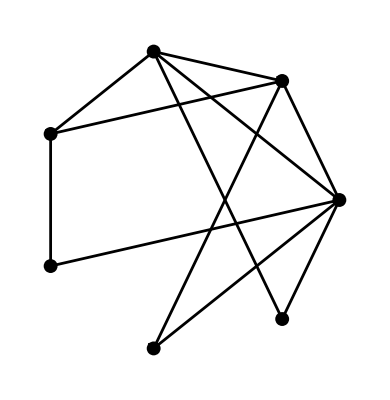

```mathematica
ShowLabeledGraph[G5]
```

```mathematica
HamiltonianQ[G5]
```

False

El següent teorema de Dirac dóna una condició suficient per a que un graf G sigui Hamiltonià a partir de la llista dels graus dels seus vèrtexs.
                                   
                                             TEOREMA DE DIRAC:
Sigui G un graf connex amb n vèrtexs, on  n≥ 3.
Si el grau de cada vèrtex de G és ≥ n/2  aleshores G és hamiltonià.

Observeu que els grafs G2 i G3 definits anteriorment satisfan les hipòtesis del teorema anterior, la qual cosa no ens sorprèn ja que hem vist que són hamiltonians.

Tanmateix les hipòtesis del Teorema de Dirac no són necessàries. Per exemple:

```mathematica
G6= FromAdjacencyLists[{{2,3},{1,4,5,3},{2,4,5},{2,3,5},{1,2,4,3}}]
```

⁃Graph:<8,5,Undirected>⁃

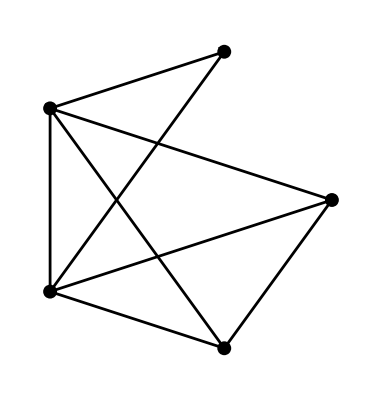

```mathematica
ShowLabeledGraph[G6]
```

```mathematica
Degrees[G6]
```

{2,4,4,3,3}

```mathematica
Hi ha un vertex de grau 2 nomes.
```

```mathematica
HamiltonianQ[G6]
```

True

Comproveu que no satisfà les hipòtesis del Teorema de Dirac, però és hamiltonià. Trobeu-ne un cicle hamiltonià.

El fet de que G6 sigui hamiltonià resulta del Teorema d’ Ore següent que millora el teorema de Dirac:                  

                                    TEOREMA D' ORE
Sigui G un graf connex amb n vèrtexs, on  n≥ 3.
Si la suma dels graus de dos vèrtexs v,w, no adjacents qualssevol de G satisfà
deg(v)+deg(w) ≥ n  aleshores G és hamiltonià.

### Exercici per trametre

Dos amics, Raul i Laura, tenen pensat anar de vacances a l’illa de Martinica. La figura adjunta representa els llocs interessants de l’illa i les carreteres que els uneixen. La Laura és una turista nata i vol visitar cada lloc un cop i tornar al punt de partida. Mentres que en Raul és un explorador nat i vol travessar cada carretera un sol cop en qualsevol direcció i no l’hi importa començar i acabar en llocs diferents. Es posible trobar rutes convenients als interessos dels dos amics? Justifiqueu les respostes amb els teoremes adequats i/o trobant el recorregut corresponent.

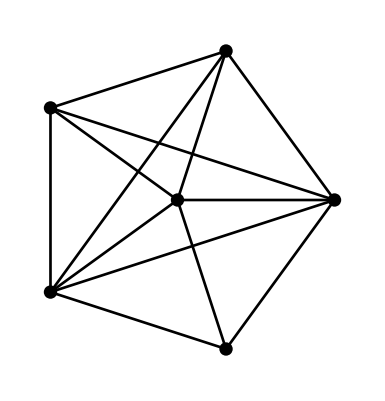

```mathematica
A1 = FromAdjacencyLists[{{2, 3, 5, 6},{1,3,5,6},{1,2,4,5,6},{3,5,6},{1,2,3,4,6},{1,2,3,4,5}}]
```

⁃Graph:<13,6,Undirected>⁃

```mathematica
Degrees[A1]
```

{4,4,5,3,5,5}

```mathematica
EulerianQ[A1]
```

False

```mathematica
HamiltonianQ[A1]
```

True

```mathematica
La Laura, que vol trobar un camí Hamiltoniá (que passi per tots els punts es igual el ordre), si té sort i por trbar un recorregut com el que vol. En Raul no té tanta sort, ja que busca un camí Euleriá (que passi per totes les carreteres, sense repetir-les) i no existeix cap.
```

## ALGORISME DE HIERHOLZER (Eulerians)

1. Fixem un circuit en G : R1. Marquem les arestes de R1. i = 1.

2. Si Ri conté totes les arestes de G : Parem.

3. Altrament : prenem vi un vèrtex de Ri incident amb una aresta ei no marcada.

4. Generem un circuit Qi començant per Vi utilitzant ei. Marquem les arestes de Qi.

5. Ri + 1 = Qi + Ri

6. i++. Tornem a 2.